### Basic Examples (2)

Generate a random mixed graph with 20 vertices and 54 edges with 0.75 directed edges:

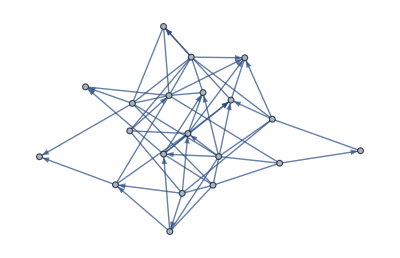

```mathematica
{{-Graphics-, RandomMixedGraph}}[{20,54},.75]
```

Create a list of 3 random mixed graphs with 20 vertices and 54 edges:

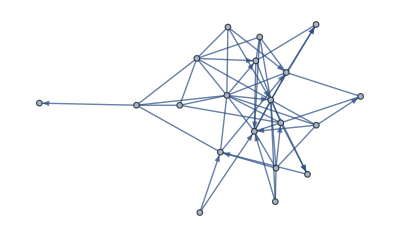
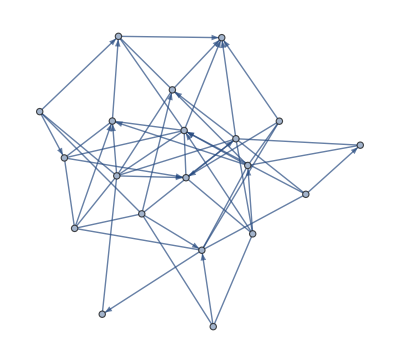
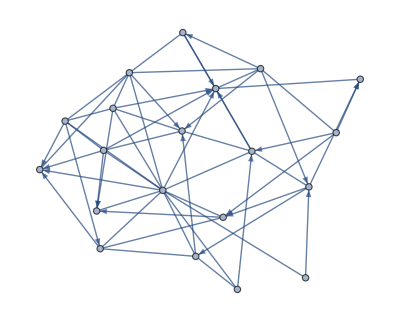

```mathematica
{{-Graphics-, RandomMixedGraph}}[{20,54},.75,3]
```

Create a random mixed graph from a graph distribution:

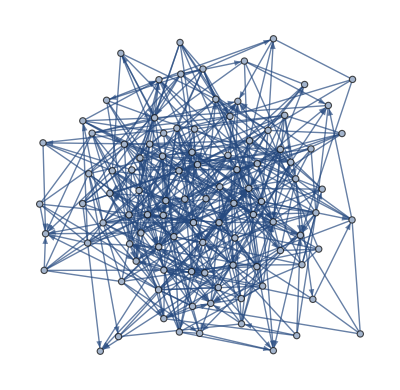

```mathematica
{{-Graphics-, RandomMixedGraph}}[BernoulliGraphDistribution[100,0.1],0.75]
```

Create a list of 3 random mixed graphs with a graph distribution:

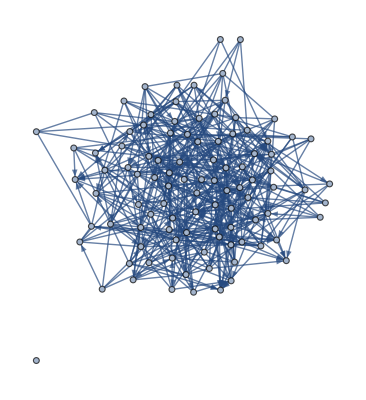
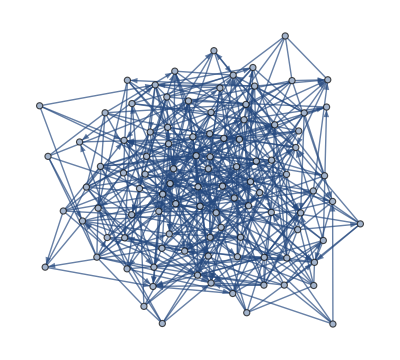
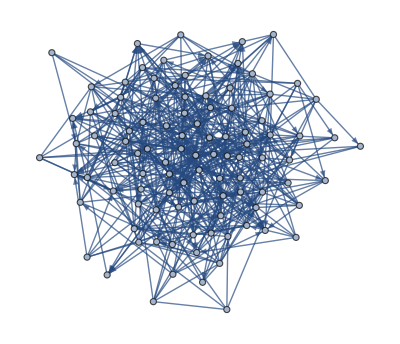

```mathematica
{{-Graphics-, RandomMixedGraph}}[BernoulliGraphDistribution[100,0.1],0.75,3]
```

### Scope (7)

Create a random mixed graph with the Barabasi-Albert graph distribution:

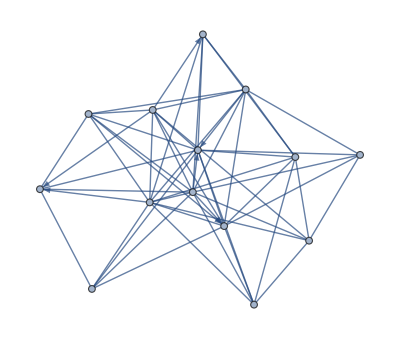

```mathematica
{{-Graphics-, RandomMixedGraph}}[BarabasiAlbertGraphDistribution[14,5],.2]
```

Create a list of mixed graphs:

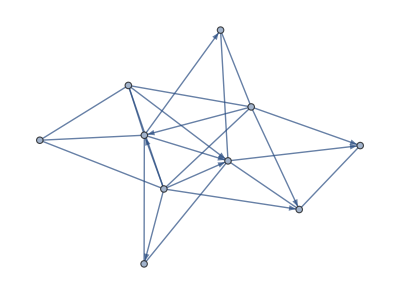
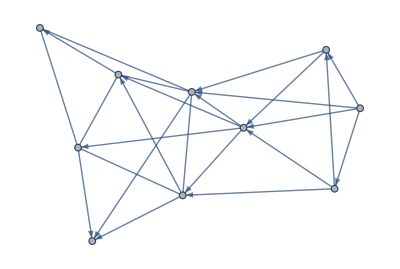
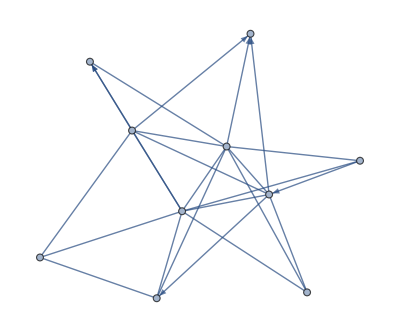
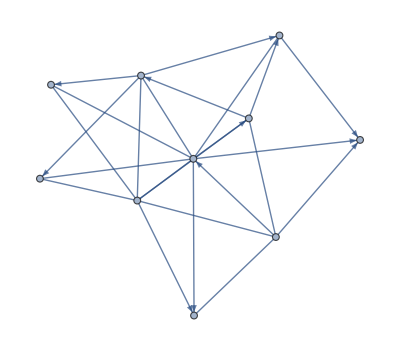

```mathematica
{{-Graphics-, RandomMixedGraph}}[BarabasiAlbertGraphDistribution[10,3],.75,4]
```

Create a mixed graph with the degree graph vertex distribution:

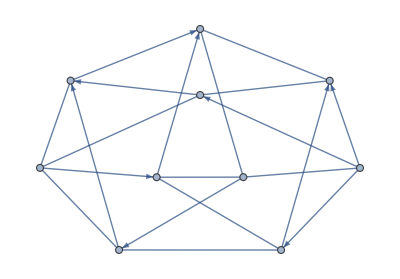

```mathematica
{{-Graphics-, RandomMixedGraph}}[DegreeGraphDistribution[{4,4,4,4,4,4,4,4,4,4}],.5]
```

Create a mixed graph with the price graph distribution based on an attractiveness parameter of 1:

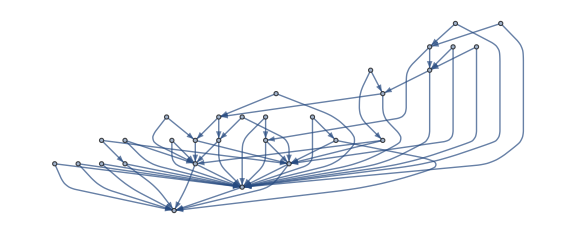

```mathematica
{{-Graphics-, RandomMixedGraph}}[PriceGraphDistribution[30,2,1],.75,ImageSize->Large]
```

Create a random mixed graph that obeys a spatial graph distribution:

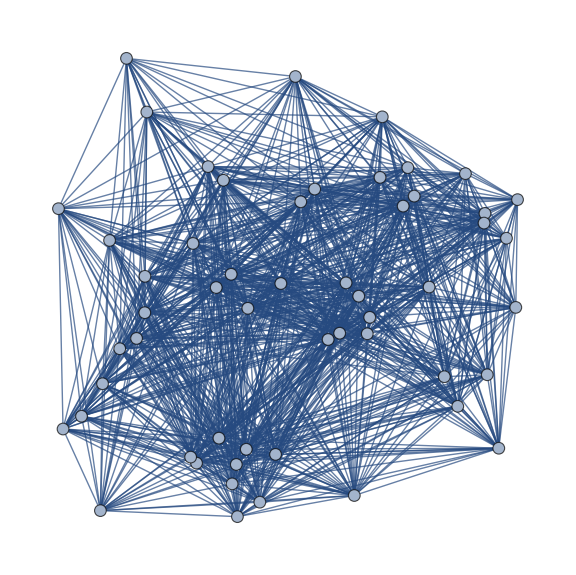

```mathematica
{{-Graphics-, RandomMixedGraph}}[SpatialGraphDistribution[54,2/3],.7,ImageSize->Large]
```

Use the uniform graph distribution for a mixed graph:

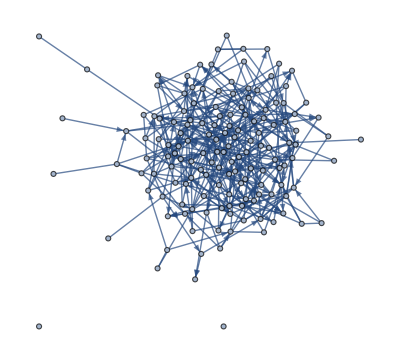

```mathematica
{{-Graphics-, RandomMixedGraph}}[UniformGraphDistribution[148,403],.7]
```

Create a random mixed graph generated with the Watts–Strogatz graph distribution:

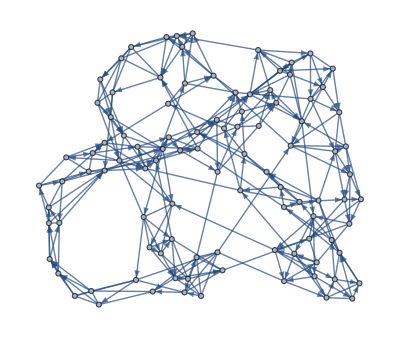

```mathematica
{{-Graphics-, RandomMixedGraph}}[WattsStrogatzGraphDistribution[100,0.1,3],.6]
```